```mathematica
OA1={{1.9882697947214076,34.76014760147601},
{2.8592375366568916,33.726937269372684}};
```

```mathematica
OA2={{2.8592375366568916,33.726937269372684},{
2.348973607038123,31.586715867158667}};
```

```mathematica
TA1={{2.348973607038123,31.586715867158667},{
3.736070381231672,29.815498154981544}};
```

```mathematica
TA2={{3.736070381231672,29.815498154981544},{
1.9882697947214076,22.50922509225092}};
```

```mathematica
SuperK={{1.9912023460410557,25.461254612546117},{
4.69208211143695,21.992619926199257}};
```

```mathematica
Stability={{1.9882697947214076,10.84870848708487},{
5.011730205278592,23.025830258302577}};
```

```mathematica
OA1plot=Plot[Interpolation[OA1][x],{x,1.9882697947214076,2.8592375366568916},PlotStyle->{Green}];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

```mathematica
OA2plot=Plot[Interpolation[OA2][x],{x,2.348973607038123,2.8592375366568916},PlotStyle->{Green}];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

```mathematica
TA1plot=Plot[Interpolation[TA1][x],{x,2.348973607038123,3.736070381231672},PlotStyle->{Green}];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

```mathematica
TA2plot=Plot[Interpolation[TA2][x],{x,1.9882697947214076,3.736070381231672},PlotStyle->{Green}];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

```mathematica
SuperKplot=Plot[Interpolation[SuperK][x],{x,1.9912023460410557,5.011730205278592},PlotStyle->{Cyan}];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

```mathematica
Stabilityplot=Plot[Interpolation[Stability][x],{x,1.9882697947214076,8},PlotStyle->{Black}];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

```mathematica
canvasQball=Plot[-1,{x,2,7.5},PlotRange->{5,70},Frame->True,FrameStyle->Black,FrameLabel->{"m_S (GeV)","Q"}];
```

#### Our constraints on Q ball

#### Explosiveness:

```mathematica
Qballboom[x_]:=38+4(x-3)
```

```mathematica
Qballflux[x_]:=60-4/3(x-3)
```

```mathematica
QballBH[x_]:=64-4(x-3)
```

```mathematica
boom=Plot[Qballboom[x],{x,2,8},PlotStyle->{Blue,Dashed}];
```

```mathematica
flux=Plot[Qballflux[x],{x,2,8},PlotStyle->{Red,Dashed}];
```

```mathematica
BH=Plot[QballBH[x],{x,2,8},PlotStyle->{Black,Dashed}];
```

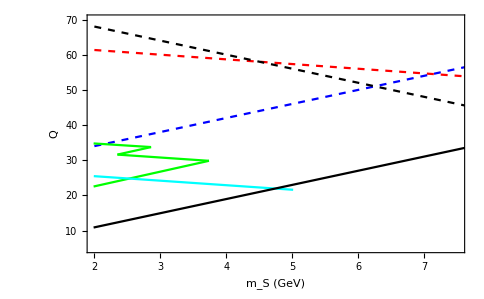

```mathematica
Show[canvasQball,boom,flux,BH,OA1plot,OA2plot,TA1plot,TA2plot,SuperKplot,Stabilityplot]
```